IncidenceGraph::inv: The argument «1» in IncidenceGraph[«1»] is not a valid incidence matrix.

MeanGraphDistance::graph: A graph object is expected at position 1 in MeanGraphDistance[IncidenceGraph[«1»]].

IncidenceGraph::inv: The argument SparseArray[Automatic,«2»,{1,{{0,2,3,5,7,10,12,13,15,18,20,22,24,26,29,31,33,35,36,37,39},{{1},{2},{3},{3},{4},{4},{5},{5},{6},{20},{6},{7},{7},{8},{9},{9},{10},«5»,{12},{13},{13},{14},{14},{15},{19},{15},{16},{16},{17},{17},{18},{18},{19},{20},{8}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}] in IncidenceGraph[«1»] is not a valid incidence matrix.

General::stop: Further output of IncidenceGraph::inv will be suppressed during this calculation.

MeanGraphDistance::graph: A graph object is expected at position 1 in MeanGraphDistance[IncidenceGraph[SparseArray[Automatic,«2»,{1,{{0,2,3,5,7,10,12,13,15,18,20,22,24,26,29,31,33,35,36,37,39},{{1},{2},{3},{3},{4},{4},{5},{5},{6},{20},{6},{7},{7},«13»,{14},{15},{19},{15},{16},{16},{17},{17},{18},{18},{19},{20},{8}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]].

MeanGraphDistance::graph: A graph object is expected at position 1 in MeanGraphDistance[IncidenceGraph[«1»]].

General::stop: Further output of MeanGraphDistance::graph will be suppressed during this calculation.

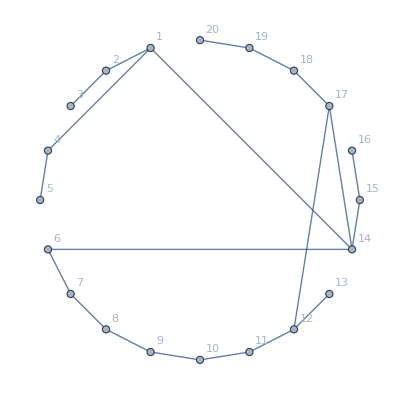
{{-Graphics-},3.75263}

```mathematica
aplMin=50000;
mMin;
(*----------Basic Setup----------*)
For[var=1,var<1000,var++,
n=20;
r=5;
(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*---m[[2,3]]=0; m[[7,3]]=1;---*)
(*----------Rewireing----------*)
(*-----m[[coloumn,row]]-----*)
outputString={{(*old*)},{(*new*)}};
Do[
mjEdge=Random[Integer,{1,n}];
For[j=1,j<n+1,j++,
If[m[[j,mjEdge]]==1 && j≠mjEdge ,
miOld=j;
];
];
Label[againRandom];
miNew=Random[Integer,{1,n}];
If[miNew == mjEdge || miNew==miOld,Goto[againRandom],Goto[check]];
Label[check];
AppendTo[outputString[[1]],{miOld,mjEdge}];
AppendTo[outputString[[2]],{miNew,mjEdge}];
m[[miOld,mjEdge]]=0;
m[[miNew,mjEdge]]=1;
,r];

(*----------------------------*)
Grid[outputString,Frame->{All,None}];


matrixLabel=Table[x,{x,n}];
(*Print[MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]];*)

IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
(*Print[Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]];*)

(*----------Average Path Length Calculation----------*)


(*----------Output----------*)
apl=MeanGraphDistance[m];
(*Print[N[apl]];*)

If[apl≠ ∞,
If[apl<aplMin,
aplMin=apl;
mMin=m;
];
]
]

Print[{Table[Graph[mMin,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}],N[aplMin]}];
```